# Official code for Extended Parrondo’s game and Brownian ratchets: Strong and weak Parrondo effect by Degang Wu and Kwok Yip Szeto

code by Degang Wu

## Run this FIrst! It will load all functions

```mathematica
(* Set current directory as needed *)
SetDirectory["~/extended_parrondo_game"]
```

/Users/wudegang/extended_parrondo_game

```mathematica
Get["coreFunctions.m"]
Get["gainExpressions.m"]
```

## Fig. 1

```mathematica
With[{T=100,p=0.5,p1=0.1,p2=0.67},
B3=bmMx[p1,p2,3,12];
B4=bmMx[p1,p2,4,12];
ListPlot[{
MapThread[{#1,#2}&,{Range[0,T],ParrondoExpected[{B3},T]}],
MapThread[{#1,#2}&,{Range[0,T][[1;;-1;;2]],MovingAverage[ParrondoExpected[{B4},T+1],2][[1;;-1;;2]]}],
MapThread[{#1,#2}&,{Range[0,T][[1;;-1;;2]],MovingAverage[ParrondoExpected[Evaluate[{C B3+(1-C)B4}/.{C->0.2}],T+1],2][[1;;-1;;2]]}],
MapThread[{#1,#2}&,{Range[0,T],MovingAverage[ParrondoExpected[{B3,B4,B3,B4,B4},T+1],2]}]
},
Joined->{True,False,False,True},
PlotLegends->Placed[PointLegend[{"B(3)","B(4)","B(3,4,C=0.2)",(*"switching B(3),B(4),B(3),B(4),B(4)"*)"34344"},LegendMarkerSize->{10,10},LabelStyle->{Bold,12},LegendLayout->{"Row",1}],{Bottom,Center}],BaseStyle->{FontWeight->"Bold",FontSize->14},
FrameLabel->{ToExpression["t",TeXForm],ToExpression["\\langle X(t)\\rangle",TeXForm]},PlotMarkers->Automatic,
PlotStyle->{Blue,Darker[Green],Red,Black},
AxesOrigin->{0,-0.8},
PlotRange->{-1.5,-0},
Frame->True,
AspectRatio->1/2]]
```

-Graphics-

## Fig. 2

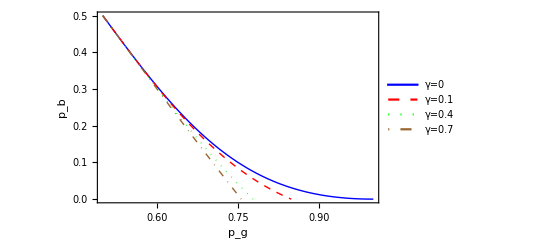

```mathematica
ContourPlot[Evaluate[{winProb[3,3]==loseProb[3,3],winProbA[3,3,γ]==loseProbA[3,3,γ]/.{γ->0.1,Subscript[p, A]->0.5},
winProbA[3,3,γ]==loseProbA[3,3,γ]/.{γ->0.4,Subscript[p, A]->0.5},
winProbA[3,3,γ]==loseProbA[3,3,γ]/.{γ->0.7,Subscript[p, A]->0.5}}
],
{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},FrameLabel->{"p_g","p_b"},ContourStyle->{Directive[Thick,Blue],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dotted],Directive[DotDashed,Thick,Brown]},PlotLegends->Placed[LineLegend[{"γ=0","γ=0.1","γ=0.4","γ=0.7"},LegendMarkerSize->{30,10},LabelStyle->{GrayLevel[0],Bold,14}],{Right,Center}],BaseStyle->{FontWeight->"Bold",FontSize->14},PlotRange->Automatic,AspectRatio->0.6]
```

## Fig. 3

```mathematica
With[{sol=Evaluate[Subscript[p, b][Subscript[p, g]]/.dBoundary[3,4,0.25]]},
Plot[{
Evaluate[(1-Subscript[p, g])^2/(Subscript[p, g]^2+(1-Subscript[p, g])^2)],Evaluate[(1-Subscript[p, g])^3/(Subscript[p, g]^3+(1-Subscript[p, g])^3)],sol
},
{Subscript[p, g],0.6,0.95},
PlotStyle->{Directive[Thick,Blue,Dashed],Directive[Thick,Red],Directive[Thick,Darker[Green],Dotted]},
PlotLegends->Placed[LineLegend[{"B(3)","B(4)","B(3,4,C=0.25)"},LegendMarkerSize->{30,10},LabelStyle->{GrayLevel[0.3],Bold,14}],{Top,Center}],BaseStyle->{FontWeight->"Bold",FontSize->14},FrameLabel->{"p_g","p_b"},
Frame->True,
Filling->{2->{{3},{White,Yellow}}}]]
```

-Graphics-

## Fig .4 (a)

```mathematica
With[{sol=Evaluate[Subscript[p, b][Subscript[p, g]]/.dBoundary[3,4,0.25]]},
Plot[{
Evaluate[(1-Subscript[p, g])^2/(Subscript[p, g]^2+(1-Subscript[p, g])^2)],Evaluate[(1-Subscript[p, g])^3/(Subscript[p, g]^3+(1-Subscript[p, g])^3)],sol
},
{Subscript[p, g],0.6,0.95},
PlotStyle->{Directive[Thick,Blue,Dashed],Directive[Thick,Red],Directive[Thick,Darker[Green],Dotted]},
PlotLegends->Placed[LineLegend[{"B(3)","B(4)","B(3,4,C=0.25)"},LegendMarkerSize->{30,10},LabelStyle->{GrayLevel[0.3],Bold,14}],{Top,Center}],BaseStyle->{FontWeight->"Bold",FontSize->14},FrameLabel->{"p_g","p_b"},
Frame->True,
Filling->{2->{{3},{White,Yellow}}}]]
```

-Graphics-

## Fig. 4 (b)

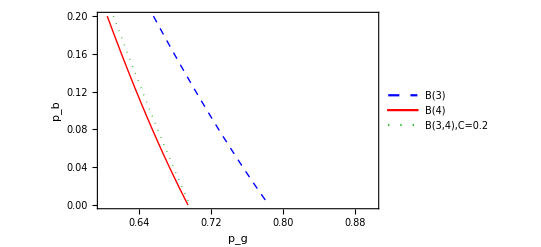

```mathematica
With[{
sol=Evaluate[Subscript[p, b][Subscript[p, g]]/.dBoundary[3,4,0.2]]
},
Plot[Evaluate[{
((1-Subscript[p, g])^(M-1)/(Subscript[p, g]^(M-1)+(1-Subscript[p, g])^(M-1))-(1/2)γ)/(1-γ)/.{M->3,Subscript[p, g]->(1-γ)Subscript[q, g]+(1/2)γ},
((1-Subscript[p, g])^(M-1)/(Subscript[p, g]^(M-1)+(1-Subscript[p, g])^(M-1))-(1/2)γ)/(1-γ)/.{M->4,Subscript[p, g]->(1-γ)Subscript[q, g]+(1/2)γ},
(sol-(1/2)γ)/(1-γ)/.{Subscript[p, g]->(1-γ)Subscript[q, g]+(1/2)γ}}/.{γ->0.35}],{Subscript[q, g],0.6,0.9},PlotRange->{0,0.2},Frame->True,
FrameLabel->{"p_g","p_b"},
BaseStyle->{FontWeight->"Bold",FontSize->18},
PlotStyle->{Directive[Thick,Blue,Dashed],Directive[Thick,Red],Directive[Thick,Darker@Green,Dotted]},
PlotLegends->Placed[LineLegend[{"B(3)","B(4)","B(3,4),C=0.2"},LegendMarkerSize->{30,10},LabelStyle->{Bold,16}],{Right,Center}],Filling->{2->{{3},{White,Yellow}}}]
]
```

## Fig. 5

```mathematica
{fairCombined34,fairCombined45,fairCombined56}=ParallelMap[winProbA[#⟦1⟧,#⟦2⟧,γ]==loseProbA[#⟦1⟧,#⟦2⟧,γ]/.{Subscript[p, b]->0,Subscript[p, A]->0.5}&,{{3,4},{4,5},{5,6}}];
{pgRule4,pgRule5,pgRule6}=ParallelMap[{Subscript[p, g]->((1/((1-γ)(1+Power[(γ(1/2))/(1-γ(1/2)),1/(M-1)]))-(γ(1/2))/(1-γ))/.{x_^y_:>If[OddQ[1/y],Surd[x,1/y], Abs[x]^y]})/.{M->#}}&,{4,5,6}];
{eq34,eq45,eq56}=ParallelMap[Simplify,{fairCombined34/.pgRule4,fairCombined45/.pgRule5,fairCombined56/.pgRule6} ];
Module[{},
Plot[{FindRoot[Evaluate[eq34/.C->Cx],{γ,0.2}]⟦1,2⟧,
FindRoot[Evaluate[eq45/.C->Cx],{γ,0.4}]⟦1,2⟧,
FindRoot[Evaluate[eq56/.C->Cx],{γ,0.4}]⟦1,2⟧},{Cx,0.01,0.99},
BaseStyle->{FontWeight->"Bold",FontSize->20},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick,Dashed],Directive[Darker[Green],Thick,Dotted],Directive[Darker[Yellow],Thick,Dashing[{Large,Small,Tiny,Small}]],Directive[Black,Thick,Dashing[{Medium,Small,Small,Small}]]},
AxesLabel->{ToExpression["C",TeXForm],ToExpression["\\gamma_{cs}",TeXForm]},
PlotLegends->Placed[LineLegend[{"B(3,4)","B(4,5)","B(5,6)"},LegendMarkerSize->{30,10},LabelStyle->{Bold,16}],{Top,Center}]]]
```

-Graphics-

## Fig. 6

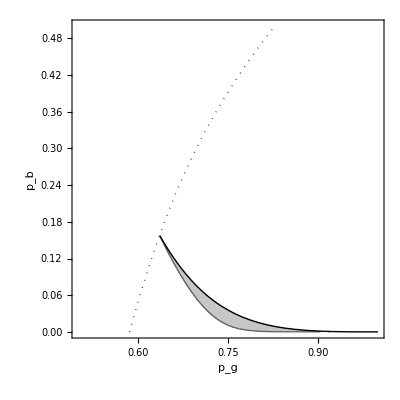

```mathematica
Show[
ContourPlot[Evaluate[winProb[3,4]-loseProb[3,4]/.C->0.2],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{ToExpression["p_g",TeXForm],ToExpression["p_b",TeXForm]},ContourStyle->{Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
RegionFunction->Function[{pg,pb},Evaluate[(gainM3x4-gainM4>0&&winProb[4,4]-loseProb[4,4]<0)/.{C->0.2,Subscript[p, g]->pg,Subscript[p, b]->pb}]],ColorFunction->(If[#1>0,Directive[Lighter@Lighter@Gray],White]&),ColorFunctionScaling->False],
ContourPlot[Evaluate[gainM3x4-gainM4/.C->0.2],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{ToExpression["p_g",TeXForm],ToExpression["p_b",TeXForm]},ContourStyle->{Black,Thick,Dotted},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None],
ContourPlot[Evaluate[winProb[4,4]-loseProb[4,4]],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{ToExpression["p_g",TeXForm],ToExpression["p_b",TeXForm]},ContourStyle->{Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None,RegionFunction->Function[{pg,pb},Evaluate[gainM3x4-gainM4/.{C->0.2,Subscript[p, g]->pg,Subscript[p, b]->pb}]>0]]
]
```

## Fig .7

```mathematica
Module[{f34=Numerator@Together[(gainAM3x4-(gainAM3x4/.{C->0}))/.{Subscript[p, g]->1,Subscript[p, b]->0,Subscript[p, A]->0.5,C->Cx}],
f45=Numerator@Together[(gainAM4x5-(gainAM4x5/.{C->0}))/.{Subscript[p, g]->1,Subscript[p, b]->0,Subscript[p, A]->0.5,C->Cx}],
ci=0.0001,ce=1-0.008,sol34,sol35,sol45},
sol34=NDSolveValue[
{D[f34/.{γ->γ[Cx]},Cx]==0,γ[ci]==(γ/.FindRoot[f34==0/.{Cx->ci},{γ,0.5}])},γ,{Cx,ci,1}];
sol45=NDSolveValue[
{D[f45/.{γ->γ[Cx]},Cx]==0,γ[ci]==(γ/.FindRoot[f45==0/.{Cx->ci},{γ,0.5}])},γ,{Cx,ci,1}];
Plot[{sol34[Cx],FindRoot[Evaluate[eq34/.C->Cx],{γ,0.2}]⟦1,2⟧,sol45[Cx],FindRoot[Evaluate[eq45/.C->Cx],{γ,0.4}]⟦1,2⟧},{Cx,ci,ce},PlotRange->{0,1},
BaseStyle->{FontWeight->"Bold",FontSize->20},
PlotStyle->{Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick,Dotted],Directive[Red,Thick,DotDashed]},
Frame->True,
FrameLabel->{ToExpression["C",TeXForm],""},
PlotLegends->Placed[LineLegend[{"B(3,4) γ_cw","B(3,4) γ_cs","B(4,5) γ_cw","B(4,5) γ_cs"},LegendMarkerSize->{30,10},LabelStyle->{Bold,15}],{Top,Center}]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolveValue::ndsz: At Cx == 0.997201, step size is effectively zero; singularity or stiff system suspected.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolveValue::ndsz: At Cx == 0.997791, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

## Fig .8

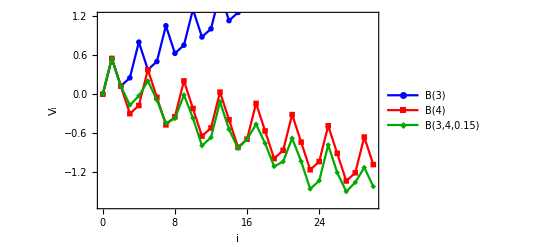

```mathematica
With[{game=C bmMx[Subscript[p, 1],Subscript[p, 2],3,12]+(1-C)bmMx[Subscript[p, 1],Subscript[p, 2],4,12]},
DiscretePlot[
{V2[x,bmMx[Subscript[p, 1],Subscript[p, 2],3,3]]/.{Subscript[p, 1]->0.1,Subscript[p, 2]->0.7},
V2[x,bmMx[Subscript[p, 1],Subscript[p, 2],4,4]]/.{Subscript[p, 1]->0.1,Subscript[p, 2]->0.7},
V2[x,game]/.{Subscript[p, 1]->0.1,Subscript[p, 2]->0.7,C->0.15}
},
{x,0,30},
PlotRange->{-1.7,1.2},
PlotMarkers->{Automatic,Medium},
Frame->True,
FrameLabel->{ToExpression["i",TeXForm],ToExpression["V_i",TeXForm]},
Joined->True,Filling->None,
BaseStyle->{FontWeight->"Bold",FontSize->20},
PlotStyle->{Directive[Blue],Directive[Red],Directive[Darker[Green]]},
PlotLegends->Placed[LineLegend[{"B(3)","B(4)","B(3,4,0.15)"},LegendMarkerSize->{20,8},LabelStyle->{Bold,15},LegendMarkers->Automatic],{Left,Center}]]
]
```

## Fig. 9 (a)

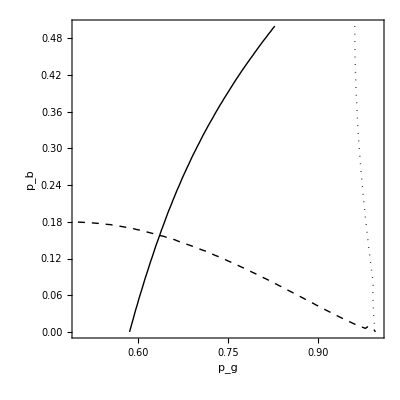

```mathematica
Show[ContourPlot[Evaluate[(gainM3x4/.{x_Subscript:>x,C->0.2})-gainM4],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{"p_g","p_b"},ContourStyle->{Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None],
With[{game=C bmMx[Subscript[p, b],Subscript[p, g],3,12]+(1-C)bmMx[Subscript[p, b],Subscript[p, g],4,12]},
ContourPlot[Evaluate[-V2[12,game/.{C->0.2}]/12+V2[4,bmMx[Subscript[p, b],Subscript[p, g],4,4]]/4],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{"p_g","p_b"},ContourStyle->{Dashed,Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None]],
With[{game=C bmMx[Subscript[p, b],Subscript[p, g],3,12]+(1-C)bmMx[Subscript[p, b],Subscript[p, g],4,12]},
ContourPlot[Evaluate[-V2[12,game/.{C->0.2}]/12+V2[3,bmMx[Subscript[p, b],Subscript[p, g],3,3]]/3],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{"p_g","p_b"},ContourStyle->{Dotted,Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None]]
]
```

## Fig. 9 (b)

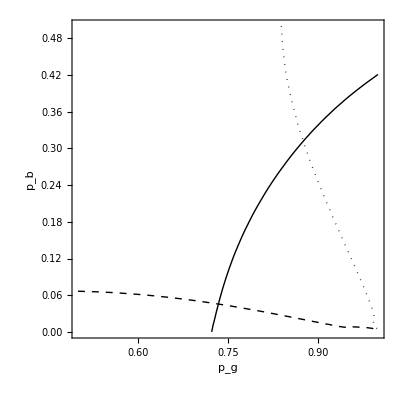

```mathematica
Show[ContourPlot[Evaluate[(gainM3x4/.{x_Subscript:>x,C->0.7})-gainM4],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{"p_g","p_b"},ContourStyle->{Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None],
With[{game=C bmMx[Subscript[p, b],Subscript[p, g],3,12]+(1-C)bmMx[Subscript[p, b],Subscript[p, g],4,12]},
ContourPlot[Evaluate[-V2[12,game/.{C->0.7}]/12+V2[4,bmMx[Subscript[p, b],Subscript[p, g],4,4]]/4],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{"p_g","p_b"},ContourStyle->{Dashed,Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None]],
With[{game=C bmMx[Subscript[p, b],Subscript[p, g],3,12]+(1-C)bmMx[Subscript[p, b],Subscript[p, g],4,12]},
ContourPlot[Evaluate[-V2[12,game/.{C->0.7}]/12+V2[3,bmMx[Subscript[p, b],Subscript[p, g],3,3]]/3],{Subscript[p, g],0.5,1},{Subscript[p, b],0,0.5},
FrameLabel->{"p_g","p_b"},ContourStyle->{Dotted,Black,Thick},Contours->{0},
BaseStyle->{FontWeight->"Bold",FontSize->16},
ContourShading->None]]
]
```